```mathematica
data=Import["../fatal-police-shootings-data.csv"];
```

```mathematica
allDates=data[[2;;, 3]];
dates=Select[allDates,StringStartsQ[#,{"2015"}]&];
counts:=Counts[dates];
days:=365;
```

```mathematica
categories=KeySort[Append[Counts[Values[counts]], 0->days-Length[counts]]];
n=Max[Keys[categories]];
For[i=1,i<n,i++,If[KeyExistsQ[categories,i],None,categories[i]=0]];
{n,categories}
```

{8,<|0→24,1→73,2→87,3→69,4→55,5→33,6→14,7→8,8→2|>}

```mathematica
k=Sum[x*categories[x],{x,Keys[categories]}]/days;
{k,N[k]}
```

{199/73,2.72603}

```mathematica
a=Map[Function[x, (ⅇ^-k k^x)/(x!)],Range[0,n-1]];
a=Append[a,1-Accumulate[a][[-1]]];
{N[a],days*N[a]}
a[[-2]]+=a[[-1]];
a=Delete[a,-1];
expect=days*a;
n=Length[expect];
{N[a],N[expect]}
```

{{0.0654789,0.178497,0.243294,0.221076,0.150665,0.0821431,0.0373207,0.0145339,0.0069918},{23.8998,65.1515,88.8024,80.6926,54.9925,29.9822,13.6221,5.30488,2.55201}}

{{0.0654789,0.178497,0.243294,0.221076,0.150665,0.0821431,0.0373207,0.0215257},{23.8998,65.1515,88.8024,80.6926,54.9925,29.9822,13.6221,7.85688}}

```mathematica
observe=Values[categories];
observe[[-2]]+=observe[[-1]];
observe=Delete[observe,-1]
```

{24,73,87,69,55,33,14,10}

```mathematica
X2=∑_(i=1)^n (expect[[i]]-observe[[i]])^2/expect[[i]];
N[X2]
```

3.57557

```mathematica
P=1-CDF[ChiSquareDistribution[n],X2];
N[P]
```

0.893246

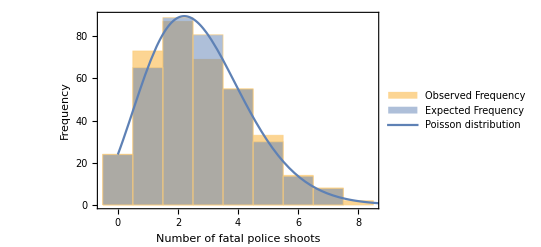

```mathematica
n=Length[observe];
weightedObserveData=WeightedData[Keys[categories],Values[categories]];
weightedExpectData=WeightedData[Range[0,n-1],expect];
fig=Show[
Histogram[
{Legended[weightedObserveData,"Observed Frequency"],
Legended[weightedExpectData,"Expected Frequency"]},n,
Frame->{True,True,False,False},
FrameTicks->{Range[0,n],Automatic},
FrameLabel->{"Number of fatal police shoots","Frequency"}
],
Plot[
Legended[Evaluate[days*PDF[PoissonDistribution[k],x]],"Poisson distribution"],{x,0,n+1},
PlotStyle->Thick,
PlotLegends->Automatic
]]
Export["q3-2015-exp.eps",fig];
```